```mathematica
<<LiteRed`;
<<Mint`;
SetDirectory[NotebookDirectory[]];
SetDim[d];
Declare[{l,r,p,q},Vector,s,Number];
sp[q,q]=0;sp[p,p]=0;
sp[q,p]=s/2;
```

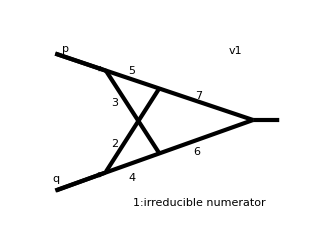
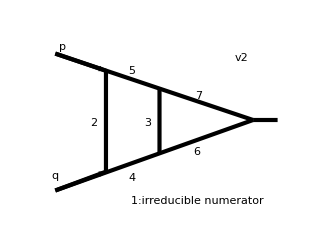
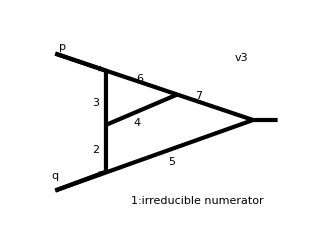

EMs→{rules_1,rules_2,…} is a an option for FindSymmetries and FindExtSymmetries. Each  rules_i is a set of substitutions which preserves the external invariants. This option helps LiteRed to find symmetries between sectors which are connect to each other by substitutions of external momenta.

FindExtSymmetries[basis_1,basis_2] finds the mappings of the sectors of basis_1 to unique sectors of basis_2. It generates the following objects:
    ExtUniqueSectors[basis_1] — the list of sectors which can not be mapped,
    ExtMappedSectors[basis_1] — the list of sectors, equivalent to some unique sectors of basis_2,
    jExtRules[basis_1,ns:(0|1)..] for each sector js[basis_1,ns:(0|1)..] in ExtMappedSectors[basis_1] — the list of rules mapping integrals to some unique sector of basis_2.
Note that FindExtSymmetries[basis_1,basis_2] requires running AnalyzeSectors[basis_1] and FindSymmetries[basis_2] beforehand. If afterwards FindExtSymmetries[basis_1,basis_3] is called, it tries to map only those sectors which are in ExtUniqueSectors[basis_1] and modifies correspondingly the lists ExtUniqueSectors[basis_1] and  ExtMappedSectors[basis_1].

FindExtSymmetries[basis_1,basis_2,…,basis_k] is a shortcut for FindExtSymmetries[basis_1,basis_k];FindExtSymmetries[basis_1,basis_(k-1)];…FindExtSymmetries[basis_1,basis_2] — pay attention to the order!

```mathematica
NewBasis[v1,{r-l,l,r,l+q,r+p,l+q-r,r+p-l},{l,r},GenerateIBP->True];
AnalyzeSectors[v1,{0,__}];
FindSymmetries[v1,EMs->{{(*p->p,q->q*)},{p->q,q->p}}];(*See EMs option descrition*)
```

```mathematica
NewBasis[v2,{r-l,l,r,l+q,l-p,l+q-r,r+p-l},{l,r},GenerateIBP->True];
AnalyzeSectors[v2,{0,__}];
FindExtSymmetries[v2,v1,EMs->{{},{p->q,q->p}}];(*See FindExtSymmetries description*)(*See EMs option descrition*)
(*This is new procedure. Omitting the option EMs->... is equivalent to EMs->{{}}*)
FindSymmetries[v2,EMs->{{(*p->p,q->q*)},{p->q,q->p}}];(*See EMs option descrition*)
```

```mathematica
NewBasis[v3,{r-q,l,r-l,r,l+q,r+p-l,l-p},{l,r},GenerateIBP->True];
AnalyzeSectors[v3,{0,__}];
FindExtSymmetries[v3,v2,v1,EMs->{{(*p->p,q->q*)},{p->q,q->p}}];(*See FindExtSymmetries description*)(*See EMs option descrition*)
(*This is new procedure. Omitting the option EMs->... is equivalent to EMs->{{}}*)
FindSymmetries[v3,EMs->{{(*p->p,q->q*)},{p->q,q->p}}];(*See EMs option descrition*)
```

```mathematica
Timing[{SolvejSector[UniqueSectors[v1]],SolvejSector[UniqueSectors[v2]],SolvejSector[UniqueSectors[v3]]}]
```

SolvejSector’s option NMIs→n, where n is some integer, prescribes SolvejSector to stop when the number of integrals not yet reducible is n
NMIs→Automatic uses Mint, if it is loaded, to determine n.

```mathematica
SetOptions[SolvejSector,NMIs->Automatic];
Timing[{SolvejSector[UniqueSectors[v1]],SolvejSector[UniqueSectors[v2]],SolvejSector[UniqueSectors[v3]]}]
```

```mathematica
IBPReduce[j[v2,-2,1,1,1,1,1,1]+j[v1,-2,1,1,1,1,1,1]+j[v3,-2,1,1,1,1,1,1]]
```